## Quadratische Korrekturfunktion

Beim Integralansatz kann bei besonders starker Schräge der Verzerrungsfaktor stark abweichen. Diese Abweichung kann mit dieser Korrektur beseitigt werden.

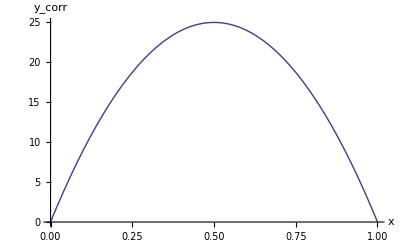

```mathematica
f[x_]:=-4h x^2+4 h x
Plot[f[x]/.h->25,{x,0,1},AxesLabel->{x,Subscript[y, corr]}]
```